## First Order Phase Transition Case 4.2: Complex Scalar in SU(2)xU(1)

```mathematica
m=.
T=.
λ=.
dmu=.
f=.
Bmu=.
W0=.

"H:"
H={Gp,(v+h+I*G0)*1/Sqrt[2]}(***)
ϕ[v_,h_,Gp_,G0_,Wp_,Z_,A_]=Sqrt[ComplexExpand[H.Conjugate[H],Gp,TargetFunctions->Conjugate]]

"∂_μ :"
Dmu=({{dmu,0},{0,dmu}}+I*g/2*{{W0,Sqrt[2]*Wp},{Sqrt[2]*Conjugate[Wp],-W0}}+I*g1/2*{{Bmu,0},{0,Bmu}})(**1/Sqrt[2]*) (*this was an extra 1/Sqrt[2] factor, mistaken when reading the notes*)

"Diagonalising B_μ and (W^0)_μ:"
Subscript[θ, w]=ArcSin[Sqrt[0.22336]]
Sin[Subscript[θ, w]]

Bmu = Cos[Subscript[θ, w]]*A-Sin[Subscript[θ, w]]*Z
W0=Sin[Subscript[θ, w]]*A+Cos[Subscript[θ, w]]*Z

"|DH|:"
DH=Dmu.H;
Kterm[v_,h_,Gp_,G0_,Wp_,Z_,A_]=Chop[Sqrt[ComplexExpand[DH.Conjugate[DH],{Gp,Wp},TargetFunctions->Conjugate]]]

"Lagrangian:"
ℒ[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_]:=Chop[Kterm[v,h,Gp,G0,Wp,Z,A]^2+-1/2*m^2*ϕ[v,h,Gp,G0,Wp,Z,A]^2+1/4*λ*ϕ[v,h,Gp,G0,Wp,Z,A]^4+f*ϕ[v,h,Gp,G0,Wp,Z,A]*ψ*OverBar[ψ]]

"Since differential operator does not contribute, momentarily setting δ=0:"
(*∂=0*)
dmu=0;

ℒ[v,h,Gp,G0,Wp,Z,A,ψ]

"Field dependent masses:"
"M_vev:"
Mv[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ],v],v]];
Subscript[M, vev][v_]=Chop[Mv[v,0,0,0,0,0,0,0]]

"M_(G^±):"
Mgpm[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ],Gp],Conjugate[Gp]]];
Subscript[M, gpm][v_]=Chop[Mgpm[v,0,0,0,0,0,0,0]]

"M_(G^0):"
Mg0[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ],G0],G0]];
Subscript[M, g0][v_]=Chop[Mg0[v,0,0,0,0,0,0,0]]

"M_(W^±):"
Mwpm[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ],Wp],Conjugate[Wp]]];
Subscript[M, wpm][v_]=Chop[Mwpm[v,0,0,0,0,0,0,0]]

"M_(W^0):"
Mz[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ],Z],Z]];
Subscript[M, Z][v_]=Chop[Mz[v,0,0,0,0,0,0,0]]

"M_A_μ:"
Mamu[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_]=Sqrt[D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ],A],A]];
Subscript[M, A][v_]=Chop[Mamu[v,0,0,0,0,0,0,0]]

"M_ψ:"
Mpsi[v_,h_,Gp_,G0_,Wp_,Z_,A_,ψ_]=D[D[ℒ[v,h,Gp,G0,Wp,Z,A,ψ],ψ],OverBar[ψ]];
Subscript[M, psi][v_]=Mpsi[v,0,0,0,0,0,0,0]


"Tree-level potential:"
Subscript[V, tree][v_]:=ℒ[v,0,0,0,0,0,0,0]
Subscript[V, tree][v]

"One-loop temperature independent corrections:"
Subscript[V, 1-loop][v_]:=1/(64*Pi^2)*(Subscript[n, vev]*(Subscript[M, vev][v])^4(Log[(Subscript[M, vev][v])^2/Q^2]-c)+Subscript[n, gpm]*(Subscript[M, gpm][v])^4(Log[(Subscript[M, gpm][v])^2/Q^2]-cb)+Subscript[n, g0]*(Subscript[M, g0][v])^4(Log[(Subscript[M, g0][v])^2/Q^2]-cb)+Subscript[n, w0]*(Subscript[M, Z][v])^4(Log[(Subscript[M, Z][v])^2/Q^2]-cb)+Subscript[n, wpm]*(Subscript[M, wpm][v])^4(Log[(Subscript[M, wpm][v])^2/Q^2]-cb)+Subscript[n, psi]*(Subscript[M, psi][v])^4(Log[(Subscript[M, psi][v])^2/Q^2]-c))

Subscript[V, 1-loop][v]

"High Temperature Expansion:"
Subscript[V, Temp][v_]:=1/(2*Pi^2)*(Subscript[n, vev]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, vev][v])^2-Pi/6*T*(Subscript[M, vev][v])^3)+Subscript[n, gpm]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, gpm][v])^2-Pi/6*T*(Subscript[M, gpm][v])^3)+Subscript[n, g0]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, g0][v])^2-Pi/6*T*(Subscript[M, g0][v])^3)+Subscript[n, w0]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, Z][v])^2-Pi/6*T*(Subscript[M, Z][v])^3)+Subscript[n, wpm]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, wpm][v])^2-Pi/6*T*(Subscript[M, wpm][v])^3)+Subscript[n, b]*((-Pi^4*T^4)/45+Pi^2/12*T^2*(Subscript[M, A][v])^2-Pi/6*T*(Subscript[M, A][v])^3)+Subscript[n, psi]((7*Pi^4*T^4)/360-Pi^2/24*T^2(Subscript[M, psi][v])^2))
Subscript[V, Temp][v]

"Effective potential:"
Subscript[V, total][v_]:=Subscript[V, tree][v]+Subscript[V, 1-loop][v]+Subscript[V, Temp][v]
Subscript[V, total][v]

V0[k_]=Subscript[V, total][k];

"Physical parameters:";
λ=0.54375;(*0.54375*)
dλ=0.1;
mtop=172; (*GeV*)
"Yukawa coupling:"
f=mtop*Sqrt[2]/Q*1.
m=125;(*93*)
Subscript[n, vev]=1;
Subscript[n, b]=2;
Subscript[n, g0]=1;
Subscript[n, gpm]=2;
Subscript[n, w0]=3;
Subscript[n, wpm]=6;
Subscript[n, psi]=-4;
(* retrived from http://www.damtp.cam.ac.uk/user/tong/qft/six.pdf*)
c=3/2;
cb=1/2;
Q=246;
e=0.303;
g=(e*1.)/Sin[Subscript[θ, w]];
g1=g*Tan[Subscript[θ, w]];
T=180(*critical temperature = 181.1221008747816*);
dT=10;

"Plotting parameters:";
min = 0;
max = 420;
step = 1;
(*
Manipulate[ListPlot[Table[Re[-1/4 m^2 v^2+(v^4 λ)/16+1/(2 π^2)(-4/45 π^4 T^4-4 ((7 π^4 T^4)/360-(π^2 T^2 √(v^2))/(24 √2))+3 (-1/45 π^4 T^4+0.20229572146755995 T^2 v^2-0.06387058878513138 T (v^2)^(3/2))+6 (-1/45 π^4 T^4+0.19236997498711159 T^2 v^2-0.05922796431853979 T (v^2)^(3/2))+1/12 π^2 T^2 (-m^2/2+(v^2 λ)/4)-1/6 π T (-m^2/2+(v^2 λ)/4)^(3/2)+1/12 π^2 T^2 (-m^2/2+(3 v^2 λ)/4)-1/6 π T (-m^2/2+(3 v^2 λ)/4)^(3/2)+2 (-1/45 π^4 T^4+1/12 π^2 T^2 (-m^2/2+(v^2 λ)/4)-1/6 π T (-m^2/2+(v^2 λ)/4)^(3/2)))+1/(64 π^2)(0.3282379780730256 v^4 (-1/2+Log[3.864991783252243*10^-6 v^2])+0.18149206883607658 v^4 (-1/2+Log[4.064414424920455*10^-6 v^2])-2 v^2 (-3/2+Log[(√(v^2))/(60516 √2)])+3 (-m^2/2+(v^2 λ)/4)^2 (-1/2+Log[(-m^2/2+(v^2 λ)/4)/60516])+(-m^2/2+(3 v^2 λ)/4)^2 (-3/2+Log[(-m^2/2+(3 v^2 λ)/4)/60516]))-(1/(2 π^2)(-4/45 π^4 T^4-4 ((7 π^4 T^4)/360)+3 (-1/45 π^4 )+6 (-1/45 π^4 T^4)+1/12 π^2 T^2 (-m^2/2)-1/6 π T (-m^2/2)^(3/2)+1/12 π^2 T^2 (-m^2/2)-1/6 π T (-m^2/2)^(3/2)+2 (-1/45 π^4 T^4+1/12 π^2 T^2 (-m^2/2)-1/6 π T (-m^2/2)^(3/2)))+1/(64 π^2)(3 (-m^2/2)^2 (-1/2+Log[(-m^2/2)/60516])+(-m^2/2)^2 (-3/2+Log[(-m^2/2)/60516])))],{v,0,max,1}],Joined-> True,DataRange->{0,max}],{T,0,1000,0.1},{λ,0,1,0.1},{m,0,200,0.1}]*)
(*Manipulate[ListPlot[Table[Re[-1/4 m^2 v^2+(v^4 λ)/16+1/(64 π^2)(0.3282379780730256 v^4 (-1/2+Log[3.864991783252243*10^-6 v^2])+0.18149206883607658 v^4 (-1/2+Log[4.064414424920455*10^-6 v^2])-2 v^2 (-3/2+Log[(√(v^2))/(60516 √2)])+3 (-m^2/2+(v^2 λ)/4)^2 (-1/2+Log[(-m^2/2+(v^2 λ)/4)/60516])+(-m^2/2+(3 v^2 λ)/4)^2 (-3/2+Log[(-m^2/2+(3 v^2 λ)/4)/60516]))],{v,0,max,1}],Joined-> True,DataRange->{0,max}],{λ,0,1,0.01},{m,125,126,0.1}]*)

(*"data:"
data=Table[1.*(Re[Limit[Subscript[V, total][v],v->j]-Limit[V0[k],k->0]]),{j,min,max,step}];(*min starts at 1 because we already know at h=0 the value is zero because of V0[k->0]*)
"Plot:"
ListPlot[data,Joined->True,AxesLabel->{v,V[v]},DataRange->{0,max}]

minval=Min[data]
pos = Position[data,minval]
"Vev value:"
(pos[[1,1]]-1)*step*1.

(*"Parameter fixing:"
"λ:"

While[Abs[(pos[[1,1]]-1)*step-Q]>0.1,If[(pos[[1,1]]-1)<Q,Print[{{"dλ",dλ=dλ/2},{"λ",λ = 1.*(λ-dλ)}, {"Min",data=Table[1.*(Re[Limit[Subscript[V, total][v],v->j]]),{j,min,max,step}];,minval = Min[data]},{"vev",pos=Position[data,minval];,(pos[[1,1]]-1)*step}}],If[(pos[[1,1]]-1)>Q,Print[{{"dλ",dλ=dλ},{"λ",λ = 1.*(λ+dλ)}, {"Min",data=Table[1.*(Re[Limit[Subscript[V, total][v],v->j]]),{j,min,max,step}];,minval = Min[data]},{"vev",pos=Position[data,minval];,(pos[[1,1]]-1)*step}}]]]]

"λ fixed:"
λ
"vev:"
vev =( pos[[1,1]]-1)*step*)

"Loop begins"
"{dT,T,min,v}"
(*only subtract by dT if minval>0 since at low temperatures, the minimum is always below negative*)

threshold = 0.01; (*the criteria in which the While loop will cease*)
ϵ=Length[data]*0.95 (* interval for finding minimum *)


If[T>1000,Print["Second Order Phase Transition"],While[Abs[minval] > threshold,If[minval>0,Print[{{"dT",dT = dT/2}, {"T",T = 1.*(T-dT)}, {"Min",data=Table[1.*(Re[Limit[Subscript[V, total][v],v->j]-Limit[V0[k],k->0]]),{j,min,max,step}];,minval = Min[Take[data,-Ceiling[ϵ]]]},{"v",pos=Position[data,minval];,pos[[1,1]]*step}}],If[minval <0, Print[{{"dT",dT},{"T",T = 1.*(T+dT)}, {"Min",data=Table[1.*(Re[Limit[Subscript[V, total][v],v->j]-Limit[V0[k],k->0]]),{j,min,max,step}];,minval = Min[Take[data,-Ceiling[ϵ]]]},{"v",pos=Position[data,minval];,pos[[1,1]]*step}}]]]]]
(*Min[Take[data,{Ceiling[pos[[1,1]]*step-ϵ],Ceiling[pos[[1,1]]*step+ϵ]}]]*)

"Loop completed"

"Critical temperature, T_c:"
T*1.

"New min:"
minval*1.

"Position and ϕ value:"
{pos[[1,1]],pos[[1,1]]*step}
data;

img1=ListPlot[data,Joined->True,AxesLabel->{v,V[v]},DataRange->{0,max}]
"Whole plot:"
img2=ListPlot[Table[1.*(Re[Subscript[V, total][v]-Limit[V0[k],k->0]]),{v,-max,max,step}],Joined->True,AxesLabel->{v,V[v]},DataRange->{-max,max}]*)

(*Export["SU(2)xU(1).jpg",img1,NotebookDirectory]
Export["SU(2)xU(1)fullplt.jpg",img2,NotebookDirectory]
*)
```

H:

{Gp,(ⅈ G0+h+v)/(√2)}

√(G0^2/2+h^2/2+h v+v^2/2+Gp Conjugate[Gp])

∂_μ :

{{(0.+0.171911 ⅈ) Bmu+dmu+(0.+0.32056 ⅈ) W0,(0.+0. ⅈ)+(0.+0.453341 ⅈ) Wp},{(0.+0. ⅈ)+(0.+0.453341 ⅈ) Conjugate[Wp],(0.+0.171911 ⅈ) Bmu+dmu-(0.+0.32056 ⅈ) W0}}

Diagonalising B_μ and (W^0)_μ:

0.49225

0.47261

0.881272 A-0.47261 Z

0.47261 A+0.881272 Z

|DH|:

√((dmu^2 G0^2)/2+(dmu^2 h^2)/2+dmu^2 h v+(dmu^2 v^2)/2+0.0661561 G0^2 Z^2+0.0661561 h^2 Z^2+0.132312 h v Z^2+0.0661561 v^2 Z^2+0.091809 A^2 Gp Conjugate[Gp]+dmu^2 Gp Conjugate[Gp]+(0.+0.0971298 ⅈ) A G0 Wp Conjugate[Gp]+0.0971298 A h Wp Conjugate[Gp]+0.0971298 A v Wp Conjugate[Gp]+0.12196 A Gp Z Conjugate[Gp]-(0.+0.0520889 ⅈ) G0 Wp Z Conjugate[Gp]-0.0520889 h Wp Z Conjugate[Gp]-0.0520889 v Wp Z Conjugate[Gp]+0.0405033 Gp Z^2 Conjugate[Gp]-(0.+0.0971298 ⅈ) A G0 Gp Conjugate[Wp]+0.0971298 A Gp h Conjugate[Wp]+0.0971298 A Gp v Conjugate[Wp]+0.102759 G0^2 Wp Conjugate[Wp]+0.102759 h^2 Wp Conjugate[Wp]+0.205518 h v Wp Conjugate[Wp]+0.102759 v^2 Wp Conjugate[Wp]+(0.+0.0520889 ⅈ) G0 Gp Z Conjugate[Wp]-0.0520889 Gp h Z Conjugate[Wp]-0.0520889 Gp v Z Conjugate[Wp]+0.205518 Gp Wp Conjugate[Gp] Conjugate[Wp])

Lagrangian:

Since differential operator does not contribute, momentarily setting δ=0:

0.0661561 G0^2 Z^2+0.0661561 h^2 Z^2+0.132312 h v Z^2+0.0661561 v^2 Z^2+0.091809 A^2 Gp Conjugate[Gp]+(0.+0.0971298 ⅈ) A G0 Wp Conjugate[Gp]+0.0971298 A h Wp Conjugate[Gp]+0.0971298 A v Wp Conjugate[Gp]+0.12196 A Gp Z Conjugate[Gp]-(0.+0.0520889 ⅈ) G0 Wp Z Conjugate[Gp]-0.0520889 h Wp Z Conjugate[Gp]-0.0520889 v Wp Z Conjugate[Gp]+0.0405033 Gp Z^2 Conjugate[Gp]-1/2 m^2 (G0^2/2+h^2/2+h v+v^2/2+Gp Conjugate[Gp])+1/4 λ (G0^2/2+h^2/2+h v+v^2/2+Gp Conjugate[Gp])^2-(0.+0.0971298 ⅈ) A G0 Gp Conjugate[Wp]+0.0971298 A Gp h Conjugate[Wp]+0.0971298 A Gp v Conjugate[Wp]+0.102759 G0^2 Wp Conjugate[Wp]+0.102759 h^2 Wp Conjugate[Wp]+0.205518 h v Wp Conjugate[Wp]+0.102759 v^2 Wp Conjugate[Wp]+(0.+0.0520889 ⅈ) G0 Gp Z Conjugate[Wp]-0.0520889 Gp h Z Conjugate[Wp]-0.0520889 Gp v Z Conjugate[Wp]+0.205518 Gp Wp Conjugate[Gp] Conjugate[Wp]+f ψ √(G0^2/2+h^2/2+h v+v^2/2+Gp Conjugate[Gp]) ψ̄

Field dependent masses:

M_vev:

√(-m^2/2+(3 v^2 λ)/4)

M_(G^±):

√(-m^2/2+(v^2 λ)/4)

M_(G^0):

√(-m^2/2+(v^2 λ)/4)

M_(W^±):

0.32056 √(v^2)

M_(W^0):

0.363748 √(v^2)

M_A_μ:

0

M_ψ:

(f √(v^2))/(√2)

Tree-level potential:

-1/4 m^2 v^2+(v^4 λ)/16

One-loop temperature independent corrections:

1/(64 π^2)(0.0633565 v^4 (-1/2+Log[1.69805×10^-6 v^2])+0.0525196 v^4 (-1/2+Log[2.1864×10^-6 v^2])-f^4 v^4 (-3/2+Log[(f^2 v^2)/121032])+3 (-m^2/2+(v^2 λ)/4)^2 (-1/2+Log[(-m^2/2+(v^2 λ)/4)/60516])+(-m^2/2+(3 v^2 λ)/4)^2 (-3/2+Log[(-m^2/2+(3 v^2 λ)/4)/60516]))

High Temperature Expansion:

1/(2 π^2)(-4/45 π^4 T^4-4 ((7 π^4 T^4)/360-1/48 f^2 π^2 T^2 v^2)+3 (-1/45 π^4 T^4+0.108822 T^2 v^2-0.0251999 T (v^2)^(3/2))+6 (-1/45 π^4 T^4+0.0845159 T^2 v^2-0.0172476 T (v^2)^(3/2))+1/12 π^2 T^2 (-m^2/2+(v^2 λ)/4)-1/6 π T (-m^2/2+(v^2 λ)/4)^(3/2)+1/12 π^2 T^2 (-m^2/2+(3 v^2 λ)/4)-1/6 π T (-m^2/2+(3 v^2 λ)/4)^(3/2)+2 (-1/45 π^4 T^4+1/12 π^2 T^2 (-m^2/2+(v^2 λ)/4)-1/6 π T (-m^2/2+(v^2 λ)/4)^(3/2)))

Effective potential:

-1/4 m^2 v^2+(v^4 λ)/16+1/(2 π^2)(-4/45 π^4 T^4-4 ((7 π^4 T^4)/360-1/48 f^2 π^2 T^2 v^2)+3 (-1/45 π^4 T^4+0.108822 T^2 v^2-0.0251999 T (v^2)^(3/2))+6 (-1/45 π^4 T^4+0.0845159 T^2 v^2-0.0172476 T (v^2)^(3/2))+1/12 π^2 T^2 (-m^2/2+(v^2 λ)/4)-1/6 π T (-m^2/2+(v^2 λ)/4)^(3/2)+1/12 π^2 T^2 (-m^2/2+(3 v^2 λ)/4)-1/6 π T (-m^2/2+(3 v^2 λ)/4)^(3/2)+2 (-1/45 π^4 T^4+1/12 π^2 T^2 (-m^2/2+(v^2 λ)/4)-1/6 π T (-m^2/2+(v^2 λ)/4)^(3/2)))+1/(64 π^2)(0.0633565 v^4 (-1/2+Log[1.69805×10^-6 v^2])+0.0525196 v^4 (-1/2+Log[2.1864×10^-6 v^2])-f^4 v^4 (-3/2+Log[(f^2 v^2)/121032])+3 (-m^2/2+(v^2 λ)/4)^2 (-1/2+Log[(-m^2/2+(v^2 λ)/4)/60516])+(-m^2/2+(3 v^2 λ)/4)^2 (-3/2+Log[(-m^2/2+(3 v^2 λ)/4)/60516]))

Yukawa coupling:

0.9888

```mathematica
0.0330780667122159 G0^2 Z^2+0.0330780667122159 h^2 Z^2+0.0661561334244318 h v Z^2+0.0330780667122159 v^2 Z^2+0.04590449999999999 A^2 Gp Conjugate[Gp]+(0.+0.0485649074238574 ⅈ) A G0 Wp Conjugate[Gp]+0.0485649074238574 A h Wp Conjugate[Gp]+0.0485649074238574 A v Wp Conjugate[Gp]+0.06098003301185821 A Gp Z Conjugate[Gp]-(0.+0.02604446186224605 ⅈ) G0 Wp Z Conjugate[Gp]-0.02604446186224605 h Wp Z Conjugate[Gp]-0.02604446186224605 v Wp Z Conjugate[Gp]+0.0202516334244318 Gp Z^2 Conjugate[Gp]-1/2 m^2 (G0^2/2+h^2/2+h v+v^2/2+Gp Conjugate[Gp])+1/4 λ (G0^2/2+h^2/2+h v+v^2/2+Gp Conjugate[Gp])^2-(0.+0.0485649074238574 ⅈ) A G0 Gp Conjugate[Wp]+0.0485649074238574 A Gp h Conjugate[Wp]+0.0485649074238574 A Gp v Conjugate[Wp]+0.05137949946275072 G0^2 Wp Conjugate[Wp]+0.05137949946275072 h^2 Wp Conjugate[Wp]+0.10275899892550144 h v Wp Conjugate[Wp]+0.05137949946275072 v^2 Wp Conjugate[Wp]+(0.+0.02604446186224605 ⅈ) G0 Gp Z Conjugate[Wp]-0.02604446186224605 Gp h Z Conjugate[Wp]-0.02604446186224605 Gp v Z Conjugate[Wp]+0.10275899892550143 Gp Wp Conjugate[Gp] Conjugate[Wp]+f ψ √(G0^2/2+h^2/2+h v+v^2/2+Gp Conjugate[Gp]) ψ̄
```

0.0330781 G0^2 Z^2+0.0330781 h^2 Z^2+0.0661561 h v Z^2+0.0330781 v^2 Z^2+0.0459045 A^2 Gp Conjugate[Gp]+(0.+0.0485649 ⅈ) A G0 Wp Conjugate[Gp]+0.0485649 A h Wp Conjugate[Gp]+0.0485649 A v Wp Conjugate[Gp]+0.06098 A Gp Z Conjugate[Gp]-(0.+0.0260445 ⅈ) G0 Wp Z Conjugate[Gp]-0.0260445 h Wp Z Conjugate[Gp]-0.0260445 v Wp Z Conjugate[Gp]+0.0202516 Gp Z^2 Conjugate[Gp]-15625/2 (G0^2/2+h^2/2+h v+v^2/2+Gp Conjugate[Gp])+0.135938 (G0^2/2+h^2/2+h v+v^2/2+Gp Conjugate[Gp])^2-(0.+0.0485649 ⅈ) A G0 Gp Conjugate[Wp]+0.0485649 A Gp h Conjugate[Wp]+0.0485649 A Gp v Conjugate[Wp]+0.0513795 G0^2 Wp Conjugate[Wp]+0.0513795 h^2 Wp Conjugate[Wp]+0.102759 h v Wp Conjugate[Wp]+0.0513795 v^2 Wp Conjugate[Wp]+(0.+0.0260445 ⅈ) G0 Gp Z Conjugate[Wp]-0.0260445 Gp h Z Conjugate[Wp]-0.0260445 Gp v Z Conjugate[Wp]+0.102759 Gp Wp Conjugate[Gp] Conjugate[Wp]+0.991329 ψ √(G0^2/2+h^2/2+h v+v^2/2+Gp Conjugate[Gp]) ψ̄

```mathematica
{{(dmu+(ⅈ b g1)/2+(ⅈ g W0)/2)/(√2),(ⅈ g Wp)/2},{(ⅈ g Wm)/2,(dmu+(ⅈ b g1)/2-(ⅈ g W0)/2)/(√2)}}
```

```mathematica
{{(dmu+Conjugate[(ⅈ b g1)/2+(ⅈ g W0)/2])/(√2),-1/2 ⅈ g Conjugate[Wp]},{-1/2 ⅈ g Conjugate[Wm],(dmu+Conjugate[(ⅈ b g1)/2-(ⅈ g W0)/2])/(√2)}}
```

DH:

```mathematica
{(Gp (dmu+(ⅈ b g1)/2+(ⅈ g W0)/2))/(√2)+(ⅈ g (ⅈ G0+h+v) Wp)/(2 √2),1/2 (ⅈ G0+h+v) (dmu+(ⅈ b g1)/2-(ⅈ g W0)/2)+1/2 ⅈ g Gp Wm}
```

```mathematica
√((dmu^2 G0^2)/4+1/16 b^2 G0^2 g1^2+(dmu^2 Gp^2)/2+1/8 b^2 g1^2 Gp^2+(dmu^2 h^2)/4+1/16 b^2 g1^2 h^2+1/2 dmu^2 h v+1/8 b^2 g1^2 h v+(dmu^2 v^2)/4+1/16 b^2 g1^2 v^2-1/8 b g G0^2 g1 W0+1/4 b g g1 Gp^2 W0-1/8 b g g1 h^2 W0-1/4 b g g1 h v W0-1/8 b g g1 v^2 W0+1/16 g^2 G0^2 W0^2+1/8 g^2 Gp^2 W0^2+1/16 g^2 h^2 W0^2+1/8 g^2 h v W0^2+1/16 g^2 v^2 W0^2+1/2 dmu g G0 Gp Wm+1/4 b g g1 Gp h Wm+1/4 b g g1 Gp v Wm-1/4 g^2 Gp h W0 Wm-1/4 g^2 Gp v W0 Wm+1/4 g^2 Gp^2 Wm^2-1/2 dmu g G0 Gp Wp+1/4 b g g1 Gp h Wp+1/4 b g g1 Gp v Wp+1/4 g^2 Gp h W0 Wp+1/4 g^2 Gp v W0 Wp+1/8 g^2 G0^2 Wp^2+1/8 g^2 h^2 Wp^2+1/4 g^2 h v Wp^2+1/8 g^2 v^2 Wp^2)
```

```mathematica
ComplexExpand[z+x+I*y,z]
```

x+ⅈ (y+Im[z])+Re[z]

```mathematica
v=246
g
g1
1/2*Sqrt[2*0.059433404470803364 g^2 v^2+2*0.0030665955291966293 g1^2 v^2]
```

246

1.3679

0.310719

58.0854

```mathematica
Sqrt[g^2 v^2  + g g1 v^2+ g1^2 v^2]/2
```

190.262

181.122

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

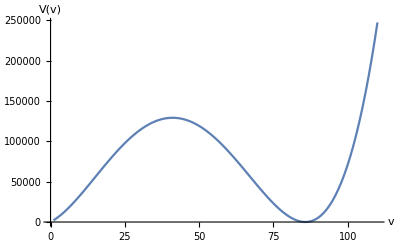

```mathematica
T
img3=ListPlot[Table[1.*(Re[Subscript[V, total][v]-Limit[V0[k],k->0]]),{v,0,110,step}],Joined->True,AxesLabel->{v,V[v]},DataRange->{0,110}]
img4=ListPlot[Table[1.*(Re[Subscript[V, total][v]-Limit[V0[k],k->0]]),{v,-0,110,step}],Joined->True,AxesLabel->{v,V[v]},DataRange->{0,110}]
```

```mathematica
60/420*100*1.
```

14.2857

```mathematica
420-95/100*420
```

21